# Effet Stark

```mathematica
Clear[]
Off[General::"spell1"]
<<"Units`"
<<"PhysicalConstants`"
$MaxPrecision=150;$MachinePrecision;$MaxExtraPrecision=150;$MaxMachineNumber;
```

### Rb^87 data and other constants

Natural constants

```mathematica
hbar=1.054571596*10^-34; (*Js, ref. Steck*)
Head[hbar];
SetPrecision[hbar,15]; (*to show hbar with 15 numbers*)
Precision[hbar] (*hbar is given in Machine Precision*);
h=hbar*2.*π;
Subscript[μ, 0]=4.*π*10^-7 ; (*N/A^2, exact, ref. Steck*)
c=2.99792458*10^8; (*m/s, exact, ref. Steck*)
Subscript[ϵ, 0]=(Subscript[μ, 0] c^2)^-1; (*F/m, exact, ref. Steck*)
Subscript[k, B]=1.3806503*10^-23 ;(*J/K, ref. Steck*)
Subscript[m, e]=9.10938188*10^-31 (*ElectronMass [kg], ref. Steck*);
Subscript[e, SI]=1.602176462*10^-19 (*ElectronCharge [C], ref. Steck*);
Subscript[e, cgs]=Subscript[e, SI]/(4.π Subscript[ϵ, 0])^(1/2);
Subscript[a, 0]=0.5291772083*10^-10; (*m , Bohr Radius, ref. Steck*)
hbar^2/(Subscript[m, e]*Subscript[e, cgs]^2) (*Subscript[a, 0] calculated*);
Subscript[e, cgs]^2/Subscript[a, 0]/Subscript[e, SI] (*atomic energy unit given in [eV=Subscript[e, SI] V]*)
Subscript[μ, B]=9.27400899*10^-24 ;(*J/T , Bohr Magneton, ref. Steck*)
u=1.66053873*10^-27 ;(*kg, Atomic mass unit , ref. Steck*)
α=Subscript[e, SI]^2/(hbar c 4. π Subscript[ϵ, 0]);
SetPrecision[α,9];
Subscript[R, ∞]=(α^2 Subscript[m, e] c)/(4.π hbar) ;(* Rydberg constant: Wikipedia Subscript[R, ∞]=1.0973731568525(73)*10^7 m^-1, slightly different from value calculated with constants from ref. Steck *) 

SetPrecision[Subscript[R, ∞],13] (*to show Subscript[R, ∞] with 13 numbers*)

(*Rubidium*)

Subscript[m, Rb87]=86.909180520*u; (*kg, Atomic Mass^87 Rb, ref. Steck*)
Subscript[R, Rb87]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb87])^-1 ;(* Subscript[R, Rb]=109736.605 cm^-1 from PRA 67 052502 (2003) Gallagher, "where R_Rb is the Rydberg constant for the reduced electron mass in Rb" -> obviously for Rb85 !! *)
SetPrecision[Subscript[R, Rb87],9] (*to show Subscript[R, ∞] with 9 numbers*)

Subscript[m, Rb85]=84.909180520*u; (*kg, Atomic Mass^85 Rb*)
Subscript[R, Rb85]=Subscript[R, ∞]*(1+Subscript[m, e]/Subscript[m, Rb85])^-1 ;
1-(1+Subscript[m, e]/Subscript[m, Rb85])^-1 (*relative effect of reduced mass (replacing Subscript[R, ∞] by Subscript[R, Rb87]) on Energy is in the order of 6E-6*)
Null
```

27.2114

1.09737315688×10^7

1.09736623×10^7

6.46074×10^-6

### Define Functions for calculation of energy-levels without interaction

Quantum defects taken from Publica
tion T. Gallagher et al. PRA 67, 052502 (2003), n>20. nf_j and ng_j states are found in Han, Gallagher et al. PRA 74 054502 (2006)

```mathematica
Subscript[δ, 0]={3.1311804,2.6548849,2.6416737,1.34809171,1.34646572,0.0165192,0.0165437,0}
Subscript[δ, 2]={0.1784,0.2900,0.2950,-0.60286,-0.59600,-0.085,-0.086,0};


(*list of quantum defects for Rb85 et Rb87 from PRA 67, 052502 (2003) 1^st entry Subscript[ns, 1/2]: lj=1, 2^nd entry Subscript[np, 1/2]:lj=2,3^nd entry Subscript[np, 3/2]:lj=3, 4^th entry Subscript[nd, 3/2]: lj=4, 5^th entry Subscript[nd, 5/2]:lj=5, 6^th entry Subscript[nf, 5/2]:lj=6, 7^th entry Subscript[nf, 7/2]:lj=7,n>20, 8^th entry for levels with l>f quantum defect is set to zero*)

δ[lj_,n_]:=Subscript[δ, 0][[lj]]+(Subscript[δ, 2][[lj]])/(n-Subscript[δ, 0][[lj]])^2; (*Quantum defect for given lj and n for n>20, see T. Gallagher "Rydberg Atoms"*)
δ[7,41]

(*Energy of Rydberg levels with quantum defect (fine structure)*)

En[lj_,n_]:=-(Subscript[R, Rb87] c)/(n-δ[lj,n])^2 (*[Hz], Energy of Level |n,l,j> with quantum effect and mass correction *)
ERadinte[lj_,n_]:=-(0.5*(1+Subscript[m, e]/Subscript[m, Rb87])^-1)/(n-δ[lj,n])^2 (*[Unit=Atomic Energy Unit = Subscript[e, cgs]^2/Subscript[a, 0] [J] = 2 h Subscript[R, ∞] c [J] = 2*Subscript[E, Hydrogen n=1]], "Energy" as needed by "radinte.exe" of Level |n,l,j> with quantum defect and with reduced mass effect, n>20 *)
(*Effect of mass on Energylevels for Rb^87 and Rb^85*)

Enw85[lj_,n_]:=-(Subscript[R, Rb85] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb85 *)
SetPrecision[(Enw85[1,51]-Enw85[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb85 to control*);
Enw87[lj_,n_]:=-(Subscript[R, Rb87] c)/n^2 (*[Hz], Energy of Level |n,l,j> without quantum effect for Rb87 *);
SetPrecision[(Enw87[1,51]-Enw87[1,50])*10^-9,15] (*Transition Frequency in GHz for Rb87 to control*);
SetPrecision[(Enw87[1,51]-Enw87[1,50])-(Enw85[1,51]-Enw85[1,50]),15] (* Difference for Transition Frequencies in Hz for Rb87 and Rb85, effect in the order of 10kHz *)
```

{3.13118,2.65488,2.64167,1.34809,1.34647,0.0165192,0.0165437,0}

0.0164925

7597.31420898438

### Integration of C-Code for Numerov Integration to calculate radial matrix elements, Tests of accuracy by comparison to Hydrogen

Install the external program "radinte.exe" which will be used to calculate the radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration in atomic length unit [a_0^I]   with the following Mathematica syntax: "RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer]".  l1 and l2 are magnetic quantum numbers. E1 and E2 are the Energies of the levels |n,l,j> calculated with quantum defect and with mass correction in atomic energy units ([e_cgs)^2/a_0] done by ERadinte[lj_,n_].
Attention: The Real numbers E1 and E2 have to be in floating point representation, otherwise Mathlink (communication between radinte.exe and Mathematica) will hang up!! The calculation in radinte.exe is done in double precision.

```mathematica
Install["D:\\Doktorarbeit\\Simus\\Mathematica\\radinte\\radinte\\Debug\\radinte.exe"]
?RadIntE

(*Test: Comparison with existing .exe file *)
RadIntE[
  ERadinte[1,50],-0.0453211,0,1,1]
RadIntE[-0.0453211,ERadinte[1,50],1,0,1]
RadIntE[-0.03661927,ERadinte[1,50],1,0,1]
Timing[RadIntE[-0.03661928,-0.0002276161,1,0,1]]
```

LinkObject["D:\Documents\raulcteixeira\Desktop\radinte\radinte.exe",14,8]

RadIntE[E1_Real,E2_Real,l1_Integer,l2_Integer,I_Integer] calculates radial matrix element <E1,l1!R**I!E2,l2> by Numerov Integration.

0.0266815

0.0266815

-0.00761383

{0.,-0.00762856}

## | 60 p3/2, mj = 3/2 >

#### Calculation of Interaction Matrix Elements <A,B|V_vdW|A',B'> centered at |60s1/2>

text

```mathematica
(*Define Initial levels*)
(*Atom1, |n_(1,)Subscript[l, 1],Subscript[s, 1],Subscript[j, 1],Subscript[m, 1]>*)
Subscript[n, 1]=60;Subscript[l, 1]=1;Subscript[j, 1]=3/2;Subscript[m, 1]=3/2;

(*Define Function Choose to choose lj for quantum defect as a function of l and j*)
Chooselj[l_,j_]:=If[j==1/2,lj=1]/;l==0  (*s states*)
Chooselj[l_,j_]:=If[j==1/2,lj=2,lj=3]/;l==1 (*p states*)
Chooselj[l_,j_]:=If[j==3/2,lj=4,lj=5]/;l==2 (*d states*)
Chooselj[l_,j_]:=If[j==5/2,lj=6,lj=7]/;l==3 (*f states*)
Chooselj[l_,j_]:=If[j==7/2,lj=8,lj=8]/;l>3 (*higher than f states*)
lj1=Chooselj[Subscript[l, 1],Subscript[j, 1]];
Subscript[E, 12]=En[lj1,Subscript[n, 1]]

(*Set up Basis for Hilbertspace*)
Subscript[n, min]=50; Subscript[n, max]=70;

δf=100*10^9; 
lmax = 5;
Clear[NList,i,k,n,l,ljA,ljB,EA,EB,EAB,t]
t=0;
NList={};
Timing[For[i=Subscript[n, min],i≤Subscript[n, max],i++, 
	For[Subscript[l, A]=0,Subscript[l, A]≤lmax,Subscript[l, A]++,
	For[ Subscript[j, A]=Abs[Subscript[l, A]-1/2],Subscript[j, A]≤Subscript[l, A]+1/2,Subscript[j, A]++, 
			ljA=Chooselj[Subscript[l, A],Subscript[j, A]];
				EA=En[ljA,i];
				If[(Subscript[E, 12]-δf)<EA<(Subscript[E, 12]+δf),For[Subscript[m, A]=-Subscript[j, A],Subscript[m, A]≤Subscript[j, A],Subscript[m, A]++,t++;NList=Join[NList,{{i,Subscript[l, A],Subscript[j, A],Subscript[m, A],EA,(-1)^Subscript[l, A]}}]]]]
]]
]
Length[NList]

NList

(* NList is organized by the principal number n *)
NList[[Ordering[NList[[All,{1}]]]]];
```

-9.99956×10^11

{0.016,Null}

422

{{55,3,5/2,-5/2,-1.0882×10^12,-1},{55,3,5/2,-3/2,-1.0882×10^12,-1},{55,3,5/2,-1/2,-1.0882×10^12,-1},{55,3,5/2,1/2,-1.0882×10^12,-1},{55,3,5/2,3/2,-1.0882×10^12,-1},{55,3,5/2,5/2,-1.0882×10^12,-1},{55,3,7/2,-7/2,-1.0882×10^12,-1},{55,3,7/2,-5/2,-1.0882×10^12,-1},{55,3,7/2,-3/2,-1.0882×10^12,-1},{55,3,7/2,-1/2,-1.0882×10^12,-1},{55,3,7/2,1/2,-1.0882×10^12,-1},{55,3,7/2,3/2,-1.0882×10^12,-1},{55,3,7/2,5/2,-1.0882×10^12,-1},{55,3,7/2,7/2,-1.0882×10^12,-1},{55,4,7/2,-7/2,-1.08754×10^12,1},{55,4,7/2,-5/2,-1.08754×10^12,1},{55,4,7/2,-3/2,-1.08754×10^12,1},{55,4,7/2,-1/2,-1.08754×10^12,1},{55,4,7/2,1/2,-1.08754×10^12,1},{55,4,7/2,3/2,-1.08754×10^12,1},{55,4,7/2,5/2,-1.08754×10^12,1},{55,4,7/2,7/2,-1.08754×10^12,1},{55,4,9/2,-9/2,-1.08754×10^12,1},{55,4,9/2,-7/2,-1.08754×10^12,1},{55,4,9/2,-5/2,-1.08754×10^12,1},{55,4,9/2,-3/2,-1.08754×10^12,1},{55,4,9/2,-1/2,-1.08754×10^12,1},{55,4,9/2,1/2,-1.08754×10^12,1},{55,4,9/2,3/2,-1.08754×10^12,1},{55,4,9/2,5/2,-1.08754×10^12,1},{55,4,9/2,7/2,-1.08754×10^12,1},{55,4,9/2,9/2,-1.08754×10^12,1},{55,5,9/2,-9/2,-1.08754×10^12,-1},{55,5,9/2,-7/2,-1.08754×10^12,-1},{55,5,9/2,-5/2,-1.08754×10^12,-1},{55,5,9/2,-3/2,-1.08754×10^12,-1},{55,5,9/2,-1/2,-1.08754×10^12,-1},{55,5,9/2,1/2,-1.08754×10^12,-1},{55,5,9/2,3/2,-1.08754×10^12,-1},{55,5,9/2,5/2,-1.08754×10^12,-1},{55,5,9/2,7/2,-1.08754×10^12,-1},{55,5,9/2,9/2,-1.08754×10^12,-1},{55,5,11/2,-11/2,-1.08754×10^12,-1},{55,5,11/2,-9/2,-1.08754×10^12,-1},{55,5,11/2,-7/2,-1.08754×10^12,-1},{55,5,11/2,-5/2,-1.08754×10^12,-1},{55,5,11/2,-3/2,-1.08754×10^12,-1},{55,5,11/2,-1/2,-1.08754×10^12,-1},{55,5,11/2,1/2,-1.08754×10^12,-1},{55,5,11/2,3/2,-1.08754×10^12,-1},{55,5,11/2,5/2,-1.08754×10^12,-1},{55,5,11/2,7/2,-1.08754×10^12,-1},{55,5,11/2,9/2,-1.08754×10^12,-1},{55,5,11/2,11/2,-1.08754×10^12,-1},{56,3,5/2,-5/2,-1.04967×10^12,-1},{56,3,5/2,-3/2,-1.04967×10^12,-1},{56,3,5/2,-1/2,-1.04967×10^12,-1},{56,3,5/2,1/2,-1.04967×10^12,-1},{56,3,5/2,3/2,-1.04967×10^12,-1},{56,3,5/2,5/2,-1.04967×10^12,-1},{56,3,7/2,-7/2,-1.04967×10^12,-1},{56,3,7/2,-5/2,-1.04967×10^12,-1},{56,3,7/2,-3/2,-1.04967×10^12,-1},{56,3,7/2,-1/2,-1.04967×10^12,-1},{56,3,7/2,1/2,-1.04967×10^12,-1},{56,3,7/2,3/2,-1.04967×10^12,-1},{56,3,7/2,5/2,-1.04967×10^12,-1},{56,3,7/2,7/2,-1.04967×10^12,-1},{56,4,7/2,-7/2,-1.04905×10^12,1},{56,4,7/2,-5/2,-1.04905×10^12,1},{56,4,7/2,-3/2,-1.04905×10^12,1},{56,4,7/2,-1/2,-1.04905×10^12,1},{56,4,7/2,1/2,-1.04905×10^12,1},{56,4,7/2,3/2,-1.04905×10^12,1},{56,4,7/2,5/2,-1.04905×10^12,1},{56,4,7/2,7/2,-1.04905×10^12,1},{56,4,9/2,-9/2,-1.04905×10^12,1},{56,4,9/2,-7/2,-1.04905×10^12,1},{56,4,9/2,-5/2,-1.04905×10^12,1},{56,4,9/2,-3/2,-1.04905×10^12,1},{56,4,9/2,-1/2,-1.04905×10^12,1},{56,4,9/2,1/2,-1.04905×10^12,1},{56,4,9/2,3/2,-1.04905×10^12,1},{56,4,9/2,5/2,-1.04905×10^12,1},{56,4,9/2,7/2,-1.04905×10^12,1},{56,4,9/2,9/2,-1.04905×10^12,1},{56,5,9/2,-9/2,-1.04905×10^12,-1},{56,5,9/2,-7/2,-1.04905×10^12,-1},{56,5,9/2,-5/2,-1.04905×10^12,-1},{56,5,9/2,-3/2,-1.04905×10^12,-1},{56,5,9/2,-1/2,-1.04905×10^12,-1},{56,5,9/2,1/2,-1.04905×10^12,-1},{56,5,9/2,3/2,-1.04905×10^12,-1},{56,5,9/2,5/2,-1.04905×10^12,-1},{56,5,9/2,7/2,-1.04905×10^12,-1},{56,5,9/2,9/2,-1.04905×10^12,-1},{56,5,11/2,-11/2,-1.04905×10^12,-1},{56,5,11/2,-9/2,-1.04905×10^12,-1},{56,5,11/2,-7/2,-1.04905×10^12,-1},{56,5,11/2,-5/2,-1.04905×10^12,-1},{56,5,11/2,-3/2,-1.04905×10^12,-1},{56,5,11/2,-1/2,-1.04905×10^12,-1},{56,5,11/2,1/2,-1.04905×10^12,-1},{56,5,11/2,3/2,-1.04905×10^12,-1},{56,5,11/2,5/2,-1.04905×10^12,-1},{56,5,11/2,7/2,-1.04905×10^12,-1},{56,5,11/2,9/2,-1.04905×10^12,-1},{56,5,11/2,11/2,-1.04905×10^12,-1},{57,2,3/2,-3/2,-1.06221×10^12,1},{57,2,3/2,-1/2,-1.06221×10^12,1},{57,2,3/2,1/2,-1.06221×10^12,1},{57,2,3/2,3/2,-1.06221×10^12,1},{57,2,5/2,-5/2,-1.06214×10^12,1},{57,2,5/2,-3/2,-1.06214×10^12,1},{57,2,5/2,-1/2,-1.06214×10^12,1},{57,2,5/2,1/2,-1.06214×10^12,1},{57,2,5/2,3/2,-1.06214×10^12,1},{57,2,5/2,5/2,-1.06214×10^12,1},{57,3,5/2,-5/2,-1.01315×10^12,-1},{57,3,5/2,-3/2,-1.01315×10^12,-1},{57,3,5/2,-1/2,-1.01315×10^12,-1},{57,3,5/2,1/2,-1.01315×10^12,-1},{57,3,5/2,3/2,-1.01315×10^12,-1},{57,3,5/2,5/2,-1.01315×10^12,-1},{57,3,7/2,-7/2,-1.01315×10^12,-1},{57,3,7/2,-5/2,-1.01315×10^12,-1},{57,3,7/2,-3/2,-1.01315×10^12,-1},{57,3,7/2,-1/2,-1.01315×10^12,-1},{57,3,7/2,1/2,-1.01315×10^12,-1},{57,3,7/2,3/2,-1.01315×10^12,-1},{57,3,7/2,5/2,-1.01315×10^12,-1},{57,3,7/2,7/2,-1.01315×10^12,-1},{57,4,7/2,-7/2,-1.01256×10^12,1},{57,4,7/2,-5/2,-1.01256×10^12,1},{57,4,7/2,-3/2,-1.01256×10^12,1},{57,4,7/2,-1/2,-1.01256×10^12,1},{57,4,7/2,1/2,-1.01256×10^12,1},{57,4,7/2,3/2,-1.01256×10^12,1},{57,4,7/2,5/2,-1.01256×10^12,1},{57,4,7/2,7/2,-1.01256×10^12,1},{57,4,9/2,-9/2,-1.01256×10^12,1},{57,4,9/2,-7/2,-1.01256×10^12,1},{57,4,9/2,-5/2,-1.01256×10^12,1},{57,4,9/2,-3/2,-1.01256×10^12,1},{57,4,9/2,-1/2,-1.01256×10^12,1},{57,4,9/2,1/2,-1.01256×10^12,1},{57,4,9/2,3/2,-1.01256×10^12,1},{57,4,9/2,5/2,-1.01256×10^12,1},{57,4,9/2,7/2,-1.01256×10^12,1},{57,4,9/2,9/2,-1.01256×10^12,1},{57,5,9/2,-9/2,-1.01256×10^12,-1},{57,5,9/2,-7/2,-1.01256×10^12,-1},{57,5,9/2,-5/2,-1.01256×10^12,-1},{57,5,9/2,-3/2,-1.01256×10^12,-1},{57,5,9/2,-1/2,-1.01256×10^12,-1},{57,5,9/2,1/2,-1.01256×10^12,-1},{57,5,9/2,3/2,-1.01256×10^12,-1},{57,5,9/2,5/2,-1.01256×10^12,-1},{57,5,9/2,7/2,-1.01256×10^12,-1},{57,5,9/2,9/2,-1.01256×10^12,-1},{57,5,11/2,-11/2,-1.01256×10^12,-1},{57,5,11/2,-9/2,-1.01256×10^12,-1},{57,5,11/2,-7/2,-1.01256×10^12,-1},{57,5,11/2,-5/2,-1.01256×10^12,-1},{57,5,11/2,-3/2,-1.01256×10^12,-1},{57,5,11/2,-1/2,-1.01256×10^12,-1},{57,5,11/2,1/2,-1.01256×10^12,-1},{57,5,11/2,3/2,-1.01256×10^12,-1},{57,5,11/2,5/2,-1.01256×10^12,-1},{57,5,11/2,7/2,-1.01256×10^12,-1},{57,5,11/2,9/2,-1.01256×10^12,-1},{57,5,11/2,11/2,-1.01256×10^12,-1},{58,0,1/2,-1/2,-1.09275×10^12,1},{58,0,1/2,1/2,-1.09275×10^12,1},{58,1,1/2,-1/2,-1.07403×10^12,-1},{58,1,1/2,1/2,-1.07403×10^12,-1},{58,1,3/2,-3/2,-1.07351×10^12,-1},{58,1,3/2,-1/2,-1.07351×10^12,-1},{58,1,3/2,1/2,-1.07351×10^12,-1},{58,1,3/2,3/2,-1.07351×10^12,-1},{58,2,3/2,-3/2,-1.02504×10^12,1},{58,2,3/2,-1/2,-1.02504×10^12,1},{58,2,3/2,1/2,-1.02504×10^12,1},{58,2,3/2,3/2,-1.02504×10^12,1},{58,2,5/2,-5/2,-1.02498×10^12,1},{58,2,5/2,-3/2,-1.02498×10^12,1},{58,2,5/2,-1/2,-1.02498×10^12,1},{58,2,5/2,1/2,-1.02498×10^12,1},{58,2,5/2,3/2,-1.02498×10^12,1},{58,2,5/2,5/2,-1.02498×10^12,1},{58,3,5/2,-5/2,-9.78506×10^11,-1},{58,3,5/2,-3/2,-9.78506×10^11,-1},{58,3,5/2,-1/2,-9.78506×10^11,-1},{58,3,5/2,1/2,-9.78506×10^11,-1},{58,3,5/2,3/2,-9.78506×10^11,-1},{58,3,5/2,5/2,-9.78506×10^11,-1},{58,3,7/2,-7/2,-9.78506×10^11,-1},{58,3,7/2,-5/2,-9.78506×10^11,-1},{58,3,7/2,-3/2,-9.78506×10^11,-1},{58,3,7/2,-1/2,-9.78506×10^11,-1},{58,3,7/2,1/2,-9.78506×10^11,-1},{58,3,7/2,3/2,-9.78506×10^11,-1},{58,3,7/2,5/2,-9.78506×10^11,-1},{58,3,7/2,7/2,-9.78506×10^11,-1},{58,4,7/2,-7/2,-9.77949×10^11,1},{58,4,7/2,-5/2,-9.77949×10^11,1},{58,4,7/2,-3/2,-9.77949×10^11,1},{58,4,7/2,-1/2,-9.77949×10^11,1},{58,4,7/2,1/2,-9.77949×10^11,1},{58,4,7/2,3/2,-9.77949×10^11,1},{58,4,7/2,5/2,-9.77949×10^11,1},{58,4,7/2,7/2,-9.77949×10^11,1},{58,4,9/2,-9/2,-9.77949×10^11,1},{58,4,9/2,-7/2,-9.77949×10^11,1},{58,4,9/2,-5/2,-9.77949×10^11,1},{58,4,9/2,-3/2,-9.77949×10^11,1},{58,4,9/2,-1/2,-9.77949×10^11,1},{58,4,9/2,1/2,-9.77949×10^11,1},{58,4,9/2,3/2,-9.77949×10^11,1},{58,4,9/2,5/2,-9.77949×10^11,1},{58,4,9/2,7/2,-9.77949×10^11,1},{58,4,9/2,9/2,-9.77949×10^11,1},{58,5,9/2,-9/2,-9.77949×10^11,-1},{58,5,9/2,-7/2,-9.77949×10^11,-1},{58,5,9/2,-5/2,-9.77949×10^11,-1},{58,5,9/2,-3/2,-9.77949×10^11,-1},{58,5,9/2,-1/2,-9.77949×10^11,-1},{58,5,9/2,1/2,-9.77949×10^11,-1},{58,5,9/2,3/2,-9.77949×10^11,-1},{58,5,9/2,5/2,-9.77949×10^11,-1},{58,5,9/2,7/2,-9.77949×10^11,-1},{58,5,9/2,9/2,-9.77949×10^11,-1},{58,5,11/2,-11/2,-9.77949×10^11,-1},{58,5,11/2,-9/2,-9.77949×10^11,-1},{58,5,11/2,-7/2,-9.77949×10^11,-1},{58,5,11/2,-5/2,-9.77949×10^11,-1},{58,5,11/2,-3/2,-9.77949×10^11,-1},{58,5,11/2,-1/2,-9.77949×10^11,-1},{58,5,11/2,1/2,-9.77949×10^11,-1},{58,5,11/2,3/2,-9.77949×10^11,-1},{58,5,11/2,5/2,-9.77949×10^11,-1},{58,5,11/2,7/2,-9.77949×10^11,-1},{58,5,11/2,9/2,-9.77949×10^11,-1},{58,5,11/2,11/2,-9.77949×10^11,-1},{59,0,1/2,-1/2,-1.05398×10^12,1},{59,0,1/2,1/2,-1.05398×10^12,1},{59,1,1/2,-1/2,-1.03624×10^12,-1},{59,1,1/2,1/2,-1.03624×10^12,-1},{59,1,3/2,-3/2,-1.03576×10^12,-1},{59,1,3/2,-1/2,-1.03576×10^12,-1},{59,1,3/2,1/2,-1.03576×10^12,-1},{59,1,3/2,3/2,-1.03576×10^12,-1},{59,2,3/2,-3/2,-9.89788×10^11,1},{59,2,3/2,-1/2,-9.89788×10^11,1},{59,2,3/2,1/2,-9.89788×10^11,1},{59,2,3/2,3/2,-9.89788×10^11,1},{59,2,5/2,-5/2,-9.89732×10^11,1},{59,2,5/2,-3/2,-9.89732×10^11,1},{59,2,5/2,-1/2,-9.89732×10^11,1},{59,2,5/2,1/2,-9.89732×10^11,1},{59,2,5/2,3/2,-9.89732×10^11,1},{59,2,5/2,5/2,-9.89732×10^11,1},{59,3,5/2,-5/2,-9.45608×10^11,-1},{59,3,5/2,-3/2,-9.45608×10^11,-1},{59,3,5/2,-1/2,-9.45608×10^11,-1},{59,3,5/2,1/2,-9.45608×10^11,-1},{59,3,5/2,3/2,-9.45608×10^11,-1},{59,3,5/2,5/2,-9.45608×10^11,-1},{59,3,7/2,-7/2,-9.45609×10^11,-1},{59,3,7/2,-5/2,-9.45609×10^11,-1},{59,3,7/2,-3/2,-9.45609×10^11,-1},{59,3,7/2,-1/2,-9.45609×10^11,-1},{59,3,7/2,1/2,-9.45609×10^11,-1},{59,3,7/2,3/2,-9.45609×10^11,-1},{59,3,7/2,5/2,-9.45609×10^11,-1},{59,3,7/2,7/2,-9.45609×10^11,-1},{59,4,7/2,-7/2,-9.45079×10^11,1},{59,4,7/2,-5/2,-9.45079×10^11,1},{59,4,7/2,-3/2,-9.45079×10^11,1},{59,4,7/2,-1/2,-9.45079×10^11,1},{59,4,7/2,1/2,-9.45079×10^11,1},{59,4,7/2,3/2,-9.45079×10^11,1},{59,4,7/2,5/2,-9.45079×10^11,1},{59,4,7/2,7/2,-9.45079×10^11,1},{59,4,9/2,-9/2,-9.45079×10^11,1},{59,4,9/2,-7/2,-9.45079×10^11,1},{59,4,9/2,-5/2,-9.45079×10^11,1},{59,4,9/2,-3/2,-9.45079×10^11,1},{59,4,9/2,-1/2,-9.45079×10^11,1},{59,4,9/2,1/2,-9.45079×10^11,1},{59,4,9/2,3/2,-9.45079×10^11,1},{59,4,9/2,5/2,-9.45079×10^11,1},{59,4,9/2,7/2,-9.45079×10^11,1},{59,4,9/2,9/2,-9.45079×10^11,1},{59,5,9/2,-9/2,-9.45079×10^11,-1},{59,5,9/2,-7/2,-9.45079×10^11,-1},{59,5,9/2,-5/2,-9.45079×10^11,-1},{59,5,9/2,-3/2,-9.45079×10^11,-1},{59,5,9/2,-1/2,-9.45079×10^11,-1},{59,5,9/2,1/2,-9.45079×10^11,-1},{59,5,9/2,3/2,-9.45079×10^11,-1},{59,5,9/2,5/2,-9.45079×10^11,-1},{59,5,9/2,7/2,-9.45079×10^11,-1},{59,5,9/2,9/2,-9.45079×10^11,-1},{59,5,11/2,-11/2,-9.45079×10^11,-1},{59,5,11/2,-9/2,-9.45079×10^11,-1},{59,5,11/2,-7/2,-9.45079×10^11,-1},{59,5,11/2,-5/2,-9.45079×10^11,-1},{59,5,11/2,-3/2,-9.45079×10^11,-1},{59,5,11/2,-1/2,-9.45079×10^11,-1},{59,5,11/2,1/2,-9.45079×10^11,-1},{59,5,11/2,3/2,-9.45079×10^11,-1},{59,5,11/2,5/2,-9.45079×10^11,-1},{59,5,11/2,7/2,-9.45079×10^11,-1},{59,5,11/2,9/2,-9.45079×10^11,-1},{59,5,11/2,11/2,-9.45079×10^11,-1},{60,0,1/2,-1/2,-1.01724×10^12,1},{60,0,1/2,1/2,-1.01724×10^12,1},{60,1,1/2,-1/2,-1.00042×10^12,-1},{60,1,1/2,1/2,-1.00042×10^12,-1},{60,1,3/2,-3/2,-9.99956×10^11,-1},{60,1,3/2,-1/2,-9.99956×10^11,-1},{60,1,3/2,1/2,-9.99956×10^11,-1},{60,1,3/2,3/2,-9.99956×10^11,-1},{60,2,3/2,-3/2,-9.56325×10^11,1},{60,2,3/2,-1/2,-9.56325×10^11,1},{60,2,3/2,1/2,-9.56325×10^11,1},{60,2,3/2,3/2,-9.56325×10^11,1},{60,2,5/2,-5/2,-9.56272×10^11,1},{60,2,5/2,-3/2,-9.56272×10^11,1},{60,2,5/2,-1/2,-9.56272×10^11,1},{60,2,5/2,1/2,-9.56272×10^11,1},{60,2,5/2,3/2,-9.56272×10^11,1},{60,2,5/2,5/2,-9.56272×10^11,1},{60,3,5/2,-5/2,-9.14342×10^11,-1},{60,3,5/2,-3/2,-9.14342×10^11,-1},{60,3,5/2,-1/2,-9.14342×10^11,-1},{60,3,5/2,1/2,-9.14342×10^11,-1},{60,3,5/2,3/2,-9.14342×10^11,-1},{60,3,5/2,5/2,-9.14342×10^11,-1},{60,3,7/2,-7/2,-9.14343×10^11,-1},{60,3,7/2,-5/2,-9.14343×10^11,-1},{60,3,7/2,-3/2,-9.14343×10^11,-1},{60,3,7/2,-1/2,-9.14343×10^11,-1},{60,3,7/2,1/2,-9.14343×10^11,-1},{60,3,7/2,3/2,-9.14343×10^11,-1},{60,3,7/2,5/2,-9.14343×10^11,-1},{60,3,7/2,7/2,-9.14343×10^11,-1},{60,4,7/2,-7/2,-9.13839×10^11,1},{60,4,7/2,-5/2,-9.13839×10^11,1},{60,4,7/2,-3/2,-9.13839×10^11,1},{60,4,7/2,-1/2,-9.13839×10^11,1},{60,4,7/2,1/2,-9.13839×10^11,1},{60,4,7/2,3/2,-9.13839×10^11,1},{60,4,7/2,5/2,-9.13839×10^11,1},{60,4,7/2,7/2,-9.13839×10^11,1},{60,4,9/2,-9/2,-9.13839×10^11,1},{60,4,9/2,-7/2,-9.13839×10^11,1},{60,4,9/2,-5/2,-9.13839×10^11,1},{60,4,9/2,-3/2,-9.13839×10^11,1},{60,4,9/2,-1/2,-9.13839×10^11,1},{60,4,9/2,1/2,-9.13839×10^11,1},{60,4,9/2,3/2,-9.13839×10^11,1},{60,4,9/2,5/2,-9.13839×10^11,1},{60,4,9/2,7/2,-9.13839×10^11,1},{60,4,9/2,9/2,-9.13839×10^11,1},{60,5,9/2,-9/2,-9.13839×10^11,-1},{60,5,9/2,-7/2,-9.13839×10^11,-1},{60,5,9/2,-5/2,-9.13839×10^11,-1},{60,5,9/2,-3/2,-9.13839×10^11,-1},{60,5,9/2,-1/2,-9.13839×10^11,-1},{60,5,9/2,1/2,-9.13839×10^11,-1},{60,5,9/2,3/2,-9.13839×10^11,-1},{60,5,9/2,5/2,-9.13839×10^11,-1},{60,5,9/2,7/2,-9.13839×10^11,-1},{60,5,9/2,9/2,-9.13839×10^11,-1},{60,5,11/2,-11/2,-9.13839×10^11,-1},{60,5,11/2,-9/2,-9.13839×10^11,-1},{60,5,11/2,-7/2,-9.13839×10^11,-1},{60,5,11/2,-5/2,-9.13839×10^11,-1},{60,5,11/2,-3/2,-9.13839×10^11,-1},{60,5,11/2,-1/2,-9.13839×10^11,-1},{60,5,11/2,1/2,-9.13839×10^11,-1},{60,5,11/2,3/2,-9.13839×10^11,-1},{60,5,11/2,5/2,-9.13839×10^11,-1},{60,5,11/2,7/2,-9.13839×10^11,-1},{60,5,11/2,9/2,-9.13839×10^11,-1},{60,5,11/2,11/2,-9.13839×10^11,-1},{61,0,1/2,-1/2,-9.8239×10^11,1},{61,0,1/2,1/2,-9.8239×10^11,1},{61,1,1/2,-1/2,-9.66417×10^11,-1},{61,1,1/2,1/2,-9.66417×10^11,-1},{61,1,3/2,-3/2,-9.6598×10^11,-1},{61,1,3/2,-1/2,-9.6598×10^11,-1},{61,1,3/2,1/2,-9.6598×10^11,-1},{61,1,3/2,3/2,-9.6598×10^11,-1},{61,2,3/2,-3/2,-9.2453×10^11,1},{61,2,3/2,-1/2,-9.2453×10^11,1},{61,2,3/2,1/2,-9.2453×10^11,1},{61,2,3/2,3/2,-9.2453×10^11,1},{61,2,5/2,-5/2,-9.2448×10^11,1},{61,2,5/2,-3/2,-9.2448×10^11,1},{61,2,5/2,-1/2,-9.2448×10^11,1},{61,2,5/2,1/2,-9.2448×10^11,1},{61,2,5/2,3/2,-9.2448×10^11,1},{61,2,5/2,5/2,-9.2448×10^11,1},{62,0,1/2,-1/2,-9.49298×10^11,1},{62,0,1/2,1/2,-9.49298×10^11,1},{62,1,1/2,-1/2,-9.34122×10^11,-1},{62,1,1/2,1/2,-9.34122×10^11,-1},{62,1,3/2,-3/2,-9.33706×10^11,-1},{62,1,3/2,-1/2,-9.33706×10^11,-1},{62,1,3/2,1/2,-9.33706×10^11,-1},{62,1,3/2,3/2,-9.33706×10^11,-1},{63,0,1/2,-1/2,-9.1785×10^11,1},{63,0,1/2,1/2,-9.1785×10^11,1},{63,1,1/2,-1/2,-9.03419×10^11,-1},{63,1,1/2,1/2,-9.03419×10^11,-1},{63,1,3/2,-3/2,-9.03024×10^11,-1},{63,1,3/2,-1/2,-9.03024×10^11,-1},{63,1,3/2,1/2,-9.03024×10^11,-1},{63,1,3/2,3/2,-9.03024×10^11,-1}}

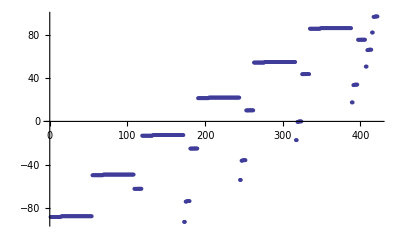

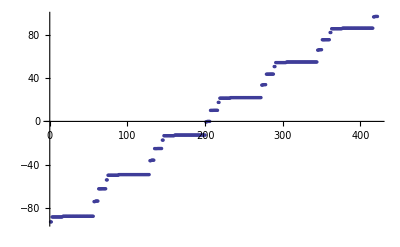

```mathematica
(*Find minimal Energydistance of found levels to initial levels*)

Clear[EDiff]
EDiff={};
For[i=1,i≤Length[NList],i++,EDiff=Join[EDiff,{(NList[[i,5]]-Subscript[E, 12])/10^9}]];
ListPlot[EDiff, PlotRange->{All,All},PlotStyle->PointSize[0.007]]
ListPlot[EDiff[[Ordering[EDiff]]], PlotRange->{All,All},PlotStyle->PointSize[0.006]]
```

```mathematica
NListTemp=NList[[Ordering[NList[[All,{5}]]]]] ;

(*Ordering NList beginning with highest Energy
LabelList is organized by energy also; it's an index for the NListTemp *)

LabelList={};
For[i=1,i≤Length[NList],i++,LabelList=Join[LabelList,{NListTemp[[i,1]]|NListTemp[[i,2]]|NListTemp[[i,3]]|NListTemp[[i,4]]}]]

(*Make List of Hilbert Space Basis level names for Plot of Energies*)

NList ;
LabelList

Clear[n,l,m,j,mj,np,lp,mp,jp,mjp,lj,ljp,Ξ,Ω,Ex,Ey,Ez,EField]
Clear[I0,E0,EFieldpi,EFieldsp,EFieldsm]

(*Calculation of r-Vector-Matrixelement <n,l,j,m|{x,y,z}|np,lp,jp,mp>(Vector) = RDip*ADip(Vector) for Angular and Radial Part (in atomic unit [Subscript[a, 0]]), ADip is a 3x1 Vector! *)
ADip[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=(√2)/2*(-1.)^(jp+l-1/2)*√(2.*jp+1)*SixJSymbol[{lp,1/2,jp},{j,1,l}]*(-1)^l*√((2*l+1)*(2*lp+1))*ThreeJSymbol[{l,0},{1,0},{lp,0}]*{ClebschGordan[{jp,mp},{1,-1},{j,m}]-ClebschGordan[{jp,mp},{1,1},{j,m}],I*ClebschGordan[{jp,mp},{1,-1},{j,m}]+I*ClebschGordan[{jp,mp},{1,1},{j,m}],√2*ClebschGordan[{jp,mp},{1,0},{j,m}]};
RDip[{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,1];

(*  Definition of Matrix Element Subscript[H, dipole]= RDip*ADip(Vector)(*.EField*) in unit [Subscript[a, 0]*Subscript[e, SI](*V/m*)]  *)
EMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_}]:=RDip[{n,l,Chooselj[l,j]},{np,lp,Chooselj[lp,jp]}]*ADip[{n,l,j,m},{np,lp,jp,mp}](*.EField*);

EMatrixelement[{60,1,3/2,3/2},{60,2,3/2,1/2}]


(*Fill up Matrix VMatrix with Sandwiched Efield Interaction <A|E*d|A'>*)
Clear[AI]
EMatrix=Array[E,{Length[NList],Length[NList]}];
EMatrix[[1,1]]
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[((Abs[NList[[i,4]]-NList[[k,4]]]==1 ∨ Abs[NList[[i,4]]-NList[[k,4]]]==0))∧(Abs[NList[[i,2]]-NList[[k,2]]]==1),EMatrix[[i,k]]=EMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]}],EMatrix[[i,k]]={0,0,0}] (*If m and l-parity*)
] 
] 
]
Clear[i,k,AI]

EMatrix[[1,1]]
```

{58|0|1/2|-1/2,58|0|1/2|1/2,55|3|7/2|-7/2,55|3|7/2|-5/2,55|3|7/2|-3/2,55|3|7/2|-1/2,55|3|7/2|1/2,55|3|7/2|3/2,55|3|7/2|5/2,55|3|7/2|7/2,55|3|5/2|-5/2,55|3|5/2|-3/2,55|3|5/2|-1/2,55|3|5/2|1/2,55|3|5/2|3/2,55|3|5/2|5/2,55|4|7/2|-7/2,55|4|7/2|-5/2,55|4|7/2|-3/2,55|4|7/2|-1/2,55|4|7/2|1/2,55|4|7/2|3/2,55|4|7/2|5/2,55|4|7/2|7/2,55|4|9/2|-9/2,55|4|9/2|-7/2,55|4|9/2|-5/2,55|4|9/2|-3/2,55|4|9/2|-1/2,55|4|9/2|1/2,55|4|9/2|3/2,55|4|9/2|5/2,55|4|9/2|7/2,55|4|9/2|9/2,55|5|9/2|-9/2,55|5|9/2|-7/2,55|5|9/2|-5/2,55|5|9/2|-3/2,55|5|9/2|-1/2,55|5|9/2|1/2,55|5|9/2|3/2,55|5|9/2|5/2,55|5|9/2|7/2,55|5|9/2|9/2,55|5|11/2|-11/2,55|5|11/2|-9/2,55|5|11/2|-7/2,55|5|11/2|-5/2,55|5|11/2|-3/2,55|5|11/2|-1/2,55|5|11/2|1/2,55|5|11/2|3/2,55|5|11/2|5/2,55|5|11/2|7/2,55|5|11/2|9/2,55|5|11/2|11/2,58|1|1/2|-1/2,58|1|1/2|1/2,58|1|3/2|-3/2,58|1|3/2|-1/2,58|1|3/2|1/2,58|1|3/2|3/2,57|2|3/2|-3/2,57|2|3/2|-1/2,57|2|3/2|1/2,57|2|3/2|3/2,57|2|5/2|-5/2,57|2|5/2|-3/2,57|2|5/2|-1/2,57|2|5/2|1/2,57|2|5/2|3/2,57|2|5/2|5/2,59|0|1/2|-1/2,59|0|1/2|1/2,56|3|7/2|-7/2,56|3|7/2|-5/2,56|3|7/2|-3/2,56|3|7/2|-1/2,56|3|7/2|1/2,56|3|7/2|3/2,56|3|7/2|5/2,56|3|7/2|7/2,56|3|5/2|-5/2,56|3|5/2|-3/2,56|3|5/2|-1/2,56|3|5/2|1/2,56|3|5/2|3/2,56|3|5/2|5/2,56|4|7/2|-7/2,56|4|7/2|-5/2,56|4|7/2|-3/2,56|4|7/2|-1/2,56|4|7/2|1/2,56|4|7/2|3/2,56|4|7/2|5/2,56|4|7/2|7/2,56|4|9/2|-9/2,56|4|9/2|-7/2,56|4|9/2|-5/2,56|4|9/2|-3/2,56|4|9/2|-1/2,56|4|9/2|1/2,56|4|9/2|3/2,56|4|9/2|5/2,56|4|9/2|7/2,56|4|9/2|9/2,56|5|9/2|-9/2,56|5|9/2|-7/2,56|5|9/2|-5/2,56|5|9/2|-3/2,56|5|9/2|-1/2,56|5|9/2|1/2,56|5|9/2|3/2,56|5|9/2|5/2,56|5|9/2|7/2,56|5|9/2|9/2,56|5|11/2|-11/2,56|5|11/2|-9/2,56|5|11/2|-7/2,56|5|11/2|-5/2,56|5|11/2|-3/2,56|5|11/2|-1/2,56|5|11/2|1/2,56|5|11/2|3/2,56|5|11/2|5/2,56|5|11/2|7/2,56|5|11/2|9/2,56|5|11/2|11/2,59|1|1/2|-1/2,59|1|1/2|1/2,59|1|3/2|-3/2,59|1|3/2|-1/2,59|1|3/2|1/2,59|1|3/2|3/2,58|2|3/2|-3/2,58|2|3/2|-1/2,58|2|3/2|1/2,58|2|3/2|3/2,58|2|5/2|-5/2,58|2|5/2|-3/2,58|2|5/2|-1/2,58|2|5/2|1/2,58|2|5/2|3/2,58|2|5/2|5/2,60|0|1/2|-1/2,60|0|1/2|1/2,57|3|7/2|-7/2,57|3|7/2|-5/2,57|3|7/2|-3/2,57|3|7/2|-1/2,57|3|7/2|1/2,57|3|7/2|3/2,57|3|7/2|5/2,57|3|7/2|7/2,57|3|5/2|-5/2,57|3|5/2|-3/2,57|3|5/2|-1/2,57|3|5/2|1/2,57|3|5/2|3/2,57|3|5/2|5/2,57|4|7/2|-7/2,57|4|7/2|-5/2,57|4|7/2|-3/2,57|4|7/2|-1/2,57|4|7/2|1/2,57|4|7/2|3/2,57|4|7/2|5/2,57|4|7/2|7/2,57|4|9/2|-9/2,57|4|9/2|-7/2,57|4|9/2|-5/2,57|4|9/2|-3/2,57|4|9/2|-1/2,57|4|9/2|1/2,57|4|9/2|3/2,57|4|9/2|5/2,57|4|9/2|7/2,57|4|9/2|9/2,57|5|9/2|-9/2,57|5|9/2|-7/2,57|5|9/2|-5/2,57|5|9/2|-3/2,57|5|9/2|-1/2,57|5|9/2|1/2,57|5|9/2|3/2,57|5|9/2|5/2,57|5|9/2|7/2,57|5|9/2|9/2,57|5|11/2|-11/2,57|5|11/2|-9/2,57|5|11/2|-7/2,57|5|11/2|-5/2,57|5|11/2|-3/2,57|5|11/2|-1/2,57|5|11/2|1/2,57|5|11/2|3/2,57|5|11/2|5/2,57|5|11/2|7/2,57|5|11/2|9/2,57|5|11/2|11/2,60|1|1/2|-1/2,60|1|1/2|1/2,60|1|3/2|-3/2,60|1|3/2|-1/2,60|1|3/2|1/2,60|1|3/2|3/2,59|2|3/2|-3/2,59|2|3/2|-1/2,59|2|3/2|1/2,59|2|3/2|3/2,59|2|5/2|-5/2,59|2|5/2|-3/2,59|2|5/2|-1/2,59|2|5/2|1/2,59|2|5/2|3/2,59|2|5/2|5/2,61|0|1/2|-1/2,61|0|1/2|1/2,58|3|7/2|-7/2,58|3|7/2|-5/2,58|3|7/2|-3/2,58|3|7/2|-1/2,58|3|7/2|1/2,58|3|7/2|3/2,58|3|7/2|5/2,58|3|7/2|7/2,58|3|5/2|-5/2,58|3|5/2|-3/2,58|3|5/2|-1/2,58|3|5/2|1/2,58|3|5/2|3/2,58|3|5/2|5/2,58|4|7/2|-7/2,58|4|7/2|-5/2,58|4|7/2|-3/2,58|4|7/2|-1/2,58|4|7/2|1/2,58|4|7/2|3/2,58|4|7/2|5/2,58|4|7/2|7/2,58|4|9/2|-9/2,58|4|9/2|-7/2,58|4|9/2|-5/2,58|4|9/2|-3/2,58|4|9/2|-1/2,58|4|9/2|1/2,58|4|9/2|3/2,58|4|9/2|5/2,58|4|9/2|7/2,58|4|9/2|9/2,58|5|9/2|-9/2,58|5|9/2|-7/2,58|5|9/2|-5/2,58|5|9/2|-3/2,58|5|9/2|-1/2,58|5|9/2|1/2,58|5|9/2|3/2,58|5|9/2|5/2,58|5|9/2|7/2,58|5|9/2|9/2,58|5|11/2|-11/2,58|5|11/2|-9/2,58|5|11/2|-7/2,58|5|11/2|-5/2,58|5|11/2|-3/2,58|5|11/2|-1/2,58|5|11/2|1/2,58|5|11/2|3/2,58|5|11/2|5/2,58|5|11/2|7/2,58|5|11/2|9/2,58|5|11/2|11/2,61|1|1/2|-1/2,61|1|1/2|1/2,61|1|3/2|-3/2,61|1|3/2|-1/2,61|1|3/2|1/2,61|1|3/2|3/2,60|2|3/2|-3/2,60|2|3/2|-1/2,60|2|3/2|1/2,60|2|3/2|3/2,60|2|5/2|-5/2,60|2|5/2|-3/2,60|2|5/2|-1/2,60|2|5/2|1/2,60|2|5/2|3/2,60|2|5/2|5/2,62|0|1/2|-1/2,62|0|1/2|1/2,59|3|7/2|-7/2,59|3|7/2|-5/2,59|3|7/2|-3/2,59|3|7/2|-1/2,59|3|7/2|1/2,59|3|7/2|3/2,59|3|7/2|5/2,59|3|7/2|7/2,59|3|5/2|-5/2,59|3|5/2|-3/2,59|3|5/2|-1/2,59|3|5/2|1/2,59|3|5/2|3/2,59|3|5/2|5/2,59|4|7/2|-7/2,59|4|7/2|-5/2,59|4|7/2|-3/2,59|4|7/2|-1/2,59|4|7/2|1/2,59|4|7/2|3/2,59|4|7/2|5/2,59|4|7/2|7/2,59|4|9/2|-9/2,59|4|9/2|-7/2,59|4|9/2|-5/2,59|4|9/2|-3/2,59|4|9/2|-1/2,59|4|9/2|1/2,59|4|9/2|3/2,59|4|9/2|5/2,59|4|9/2|7/2,59|4|9/2|9/2,59|5|9/2|-9/2,59|5|9/2|-7/2,59|5|9/2|-5/2,59|5|9/2|-3/2,59|5|9/2|-1/2,59|5|9/2|1/2,59|5|9/2|3/2,59|5|9/2|5/2,59|5|9/2|7/2,59|5|9/2|9/2,59|5|11/2|-11/2,59|5|11/2|-9/2,59|5|11/2|-7/2,59|5|11/2|-5/2,59|5|11/2|-3/2,59|5|11/2|-1/2,59|5|11/2|1/2,59|5|11/2|3/2,59|5|11/2|5/2,59|5|11/2|7/2,59|5|11/2|9/2,59|5|11/2|11/2,62|1|1/2|-1/2,62|1|1/2|1/2,62|1|3/2|-3/2,62|1|3/2|-1/2,62|1|3/2|1/2,62|1|3/2|3/2,61|2|3/2|-3/2,61|2|3/2|-1/2,61|2|3/2|1/2,61|2|3/2|3/2,61|2|5/2|-5/2,61|2|5/2|-3/2,61|2|5/2|-1/2,61|2|5/2|1/2,61|2|5/2|3/2,61|2|5/2|5/2,63|0|1/2|-1/2,63|0|1/2|1/2,60|3|7/2|-7/2,60|3|7/2|-5/2,60|3|7/2|-3/2,60|3|7/2|-1/2,60|3|7/2|1/2,60|3|7/2|3/2,60|3|7/2|5/2,60|3|7/2|7/2,60|3|5/2|-5/2,60|3|5/2|-3/2,60|3|5/2|-1/2,60|3|5/2|1/2,60|3|5/2|3/2,60|3|5/2|5/2,60|4|7/2|-7/2,60|4|7/2|-5/2,60|4|7/2|-3/2,60|4|7/2|-1/2,60|4|7/2|1/2,60|4|7/2|3/2,60|4|7/2|5/2,60|4|7/2|7/2,60|4|9/2|-9/2,60|4|9/2|-7/2,60|4|9/2|-5/2,60|4|9/2|-3/2,60|4|9/2|-1/2,60|4|9/2|1/2,60|4|9/2|3/2,60|4|9/2|5/2,60|4|9/2|7/2,60|4|9/2|9/2,60|5|9/2|-9/2,60|5|9/2|-7/2,60|5|9/2|-5/2,60|5|9/2|-3/2,60|5|9/2|-1/2,60|5|9/2|1/2,60|5|9/2|3/2,60|5|9/2|5/2,60|5|9/2|7/2,60|5|9/2|9/2,60|5|11/2|-11/2,60|5|11/2|-9/2,60|5|11/2|-7/2,60|5|11/2|-5/2,60|5|11/2|-3/2,60|5|11/2|-1/2,60|5|11/2|1/2,60|5|11/2|3/2,60|5|11/2|5/2,60|5|11/2|7/2,60|5|11/2|9/2,60|5|11/2|11/2,63|1|1/2|-1/2,63|1|1/2|1/2,63|1|3/2|-3/2,63|1|3/2|-1/2,63|1|3/2|1/2,63|1|3/2|3/2}

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, -1}, {3/2, -3/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{3/2, 1/2}, {1, 0}, {3/2, -3/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

{4.11424,0.-4.11424 ⅈ,0.}

ⅇ[1,1]

ClebschGordan::phy: ThreeJSymbol[{7/2, -7/2}, {1, -1}, {5/2, 5/2}] is not physical.

ClebschGordan::phy: ThreeJSymbol[{7/2, -7/2}, {1, 0}, {5/2, 5/2}] is not physical.

General::stop: Further output of ClebschGordan :: phy will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -7/2}, {1, -1}, {5/2, 5/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -7/2}, {1, 1}, {5/2, 5/2}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{9/2, -7/2}, {1, -1}, {5/2, 5/2}] is not triangular.

General::stop: Further output of ClebschGordan :: tri will be suppressed during this calculation.

SixJSymbol::tri: SixJSymbol[{4, 1/2, 9/2}, {5/2, 1, 3}] is not triangular.

General::stop: Further output of SixJSymbol :: tri will be suppressed during this calculation.

## Zeeman effect

1.

1.

-5.64633×10^-6

1.

-4.16989×10^-6

2

4/3

0.00139962

0.00279925

{1.95,Null}

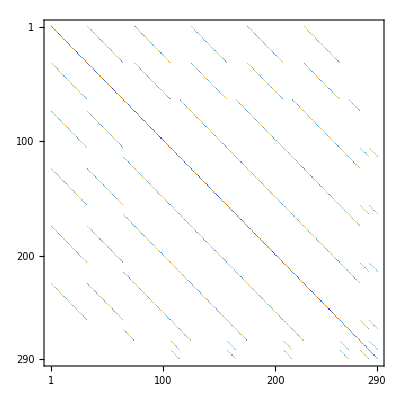

```mathematica
αB=0;
(*Calculation of Zeeman term <n,l,j,m| μ*B |np,lp,jp,mp> *)


RZeeman [{n_,l_,lj_},{np_,lp_,ljp_}]:=RadIntE[ERadinte[lj,n],ERadinte[ljp,np],l,lp,0];
RZeeman [{60,0,1},{60,0,1}]
RZeeman [{100,0,1},{100,0,1}]
RZeeman [{60,0,1},{59,0,1}]
RZeeman [{60,1,3},{60,1,3}]
RZeeman [{60,1,3},{59,1,3}]

(*Landé g-factor*)
g[l_,j_] := 3/2+(3/4-l*(l+1))/(2*j*(j+1));

g[0,1/2]
g[1,3/2]
BMatrixelement[{n_,l_,j_,m_},{np_,lp_,jp_,mp_},α_]:=RZeeman [{np,lp,Chooselj[lp,jp]},{n,l,Chooselj[l,j]}]  *  g[lp,jp]* KroneckerDelta[lp,l]*KroneckerDelta[jp,j]* (Cos[α]*mp*KroneckerDelta[mp,m]+Sin[α]/2*(Sqrt[jp*(jp+1)-mp*(mp+1)]*KroneckerDelta[mp+1,m]+Sqrt[jp*(jp+1)-mp*(mp-1)]*KroneckerDelta[mp-1,m])  );

BMatrixelement[{60,0,1/2,1/2},{60,0,1/2,1/2},0]*Subscript[μ, B]/h/10^9*10^(-4) (*Zeeman effect, GHz per Gauss, for s fine levels *)
BMatrixelement[{60,1,3/2,3/2},{60,1,3/2,3/2},0]*Subscript[μ, B]/h/10^9*10^(-4)  (*Zeeman effect, GHz per Gauss, for p 3/2 fine levels *)


(*Fill up Matrix with  <A|μ*B|A'>  *)
Clear[AI]
BMatrix=Array[B,{Length[NList],Length[NList]}];
Timing[For[i=1,i≤Length[NList],i++,
		For[k=1,k≤Length[NList],k++,
If[ (NList[[i,2]]==NList[[k,2]])&&(NList[[i,3]]==NList[[k,3]]) ,
BMatrix[[i,k]]=BMatrixelement[{NList[[i,1]],NList[[i,2]],NList[[i,3]],NList[[i,4]]},{NList[[k,1]],NList[[k,2]],NList[[k,3]],NList[[k,4]]},αB],
BMatrix[[i,k]]=0;]]
] 
] 

Clear[i,k,AI]

MatrixPlot[BMatrix]
```

{}

{-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.0882×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.08754×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04967×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.04905×10^12,-1.06221×10^12,-1.06221×10^12,-1.06221×10^12,-1.06221×10^12,-1.06214×10^12,-1.06214×10^12,-1.06214×10^12,-1.06214×10^12,-1.06214×10^12,-1.06214×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01315×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.01256×10^12,-1.09275×10^12,-1.09275×10^12,-1.07403×10^12,-1.07403×10^12,-1.07351×10^12,-1.07351×10^12,-1.07351×10^12,-1.07351×10^12,-1.02504×10^12,-1.02504×10^12,-1.02504×10^12,-1.02504×10^12,-1.02498×10^12,-1.02498×10^12,-1.02498×10^12,-1.02498×10^12,-1.02498×10^12,-1.02498×10^12,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.78506×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-9.77949×10^11,-1.05398×10^12,-1.05398×10^12,-1.03624×10^12,-1.03624×10^12,-1.03576×10^12,-1.03576×10^12,-1.03576×10^12,-1.03576×10^12,-9.89788×10^11,-9.89788×10^11,-9.89788×10^11,-9.89788×10^11,-9.89732×10^11,-9.89732×10^11,-9.89732×10^11,-9.89732×10^11,-9.89732×10^11,-9.89732×10^11,-9.45608×10^11,-9.45608×10^11,-9.45608×10^11,-9.45608×10^11,-9.45608×10^11,-9.45608×10^11,-9.45609×10^11,-9.45609×10^11,-9.45609×10^11,-9.45609×10^11,-9.45609×10^11,-9.45609×10^11,-9.45609×10^11,-9.45609×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-9.45079×10^11,-1.01724×10^12,-1.01724×10^12,-1.00042×10^12,-1.00042×10^12,-9.99956×10^11,-9.99956×10^11,-9.99956×10^11,-9.99956×10^11,-9.56325×10^11,-9.56325×10^11,-9.56325×10^11,-9.56325×10^11,-9.56272×10^11,-9.56272×10^11,-9.56272×10^11,-9.56272×10^11,-9.56272×10^11,-9.56272×10^11,-9.14342×10^11,-9.14342×10^11,-9.14342×10^11,-9.14342×10^11,-9.14342×10^11,-9.14342×10^11,-9.14343×10^11,-9.14343×10^11,-9.14343×10^11,-9.14343×10^11,-9.14343×10^11,-9.14343×10^11,-9.14343×10^11,-9.14343×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.13839×10^11,-9.8239×10^11,-9.8239×10^11,-9.66417×10^11,-9.66417×10^11,-9.6598×10^11,-9.6598×10^11,-9.6598×10^11,-9.6598×10^11,-9.2453×10^11,-9.2453×10^11,-9.2453×10^11,-9.2453×10^11,-9.2448×10^11,-9.2448×10^11,-9.2448×10^11,-9.2448×10^11,-9.2448×10^11,-9.2448×10^11,-9.49298×10^11,-9.49298×10^11,-9.34122×10^11,-9.34122×10^11,-9.33706×10^11,-9.33706×10^11,-9.33706×10^11,-9.33706×10^11,-9.1785×10^11,-9.1785×10^11,-9.03419×10^11,-9.03419×10^11,-9.03024×10^11,-9.03024×10^11,-9.03024×10^11,-9.03024×10^11}

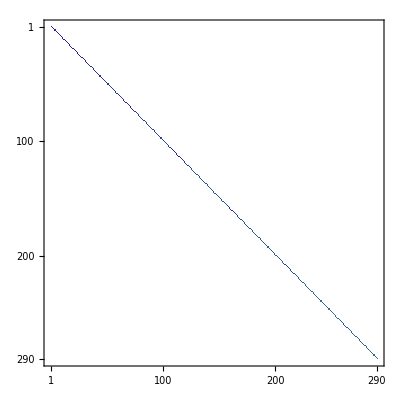

```mathematica
(*Absolute Energies of disturbed levels:*)

Clear[i,f,R]
EI={};
EI
NList;
For[i=1,i≤Length[NList],i++,EI=Join[EI,{NList[[i,5]]} ] ] ;
EIList = {} ;
EI
EIList=EI;
EI;
EI=DiagonalMatrix[EI];
MatrixPlot[EI]
```

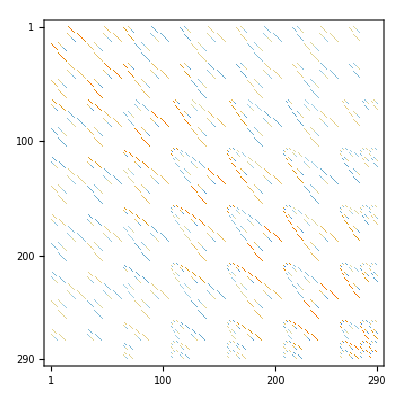

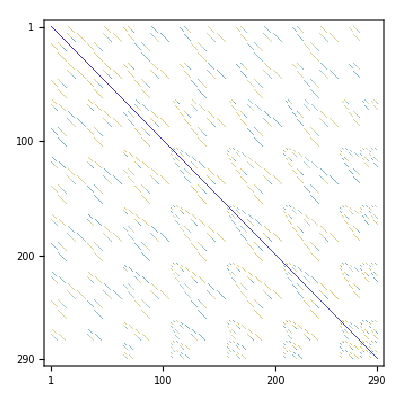

{-1092.75,-1092.75,-1088.2,-1088.2,-1088.2,-1088.2,-1088.2,-1088.2,-1088.2,-1088.2,-1088.2,-1088.2,-1088.2,-1088.2,-1088.2,-1088.2,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1087.54,-1074.03,-1074.03,-1073.51,-1073.51,-1073.51,-1073.51,-1062.21,-1062.21,-1062.21,-1062.21,-1062.14,-1062.14,-1062.14,-1062.14,-1062.14,-1062.14,-1053.98,-1053.98,-1049.67,-1049.67,-1049.67,-1049.67,-1049.67,-1049.67,-1049.67,-1049.67,-1049.67,-1049.67,-1049.67,-1049.67,-1049.67,-1049.67,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1049.05,-1036.24,-1036.24,-1035.76,-1035.76,-1035.76,-1035.76,-1025.04,-1025.04,-1025.04,-1025.04,-1024.98,-1024.98,-1024.98,-1024.98,-1024.98,-1024.98,-1017.24,-1017.24,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1013.15,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1012.56,-1000.42,-1000.42,-999.956,-999.956,-999.956,-999.956,-989.788,-989.788,-989.788,-989.788,-989.732,-989.732,-989.732,-989.732,-989.732,-989.732,-982.39,-982.39,-978.508,-978.508,-978.508,-978.508,-978.508,-978.508,-978.507,-978.507,-978.507,-978.507,-978.507,-978.507,-978.507,-978.507,-977.949,-977.949,-977.949,-977.949,-977.948,-977.948,-977.948,-977.948,-977.948,-977.948,-977.948,-977.948,-977.947,-977.947,-977.947,-977.947,-977.947,-977.947,-966.417,-966.417,-965.98,-965.98,-965.98,-965.98,-956.325,-956.325,-956.325,-956.325,-956.272,-956.272,-956.272,-956.272,-956.272,-956.272,-949.298,-949.298,-945.611,-945.611,-945.611,-945.611,-945.61,-945.61,-945.61,-945.61,-945.61,-945.61,-945.61,-945.61,-945.609,-945.609,-945.079,-945.079,-945.079,-945.079,-945.078,-945.078,-945.078,-945.078,-945.078,-945.078,-945.078,-945.078,-945.077,-945.077,-945.077,-945.077,-945.077,-945.077,-934.122,-934.122,-933.706,-933.706,-933.706,-933.706,-924.53,-924.53,-924.53,-924.53,-924.48,-924.48,-924.48,-924.48,-924.48,-924.48,-917.85,-917.85,-914.345,-914.345,-914.345,-914.345,-914.344,-914.344,-914.344,-914.344,-914.344,-914.344,-914.344,-914.344,-914.343,-914.343,-913.839,-913.839,-913.839,-913.839,-913.838,-913.838,-913.838,-913.838,-913.837,-913.837,-913.837,-913.837,-913.837,-913.837,-913.837,-913.837,-913.837,-913.837,-903.419,-903.419,-903.024,-903.024,-903.024,-903.024}

```mathematica
EField={0,0,1} ;
MatrixPlot[Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
MatrixPlot[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
Eigenvalues[EI/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]
```

{{300,-97.3806,58|0|1/2|-1/2},{300,-97.3785,58|0|1/2|1/2},{300,-96.952,55|3|7/2|-7/2},{300,-96.9514,55|3|7/2|-5/2},{300,-96.9493,55|3|7/2|-3/2},{300,-96.9491,55|3|7/2|-1/2},{300,-95.8578,55|3|7/2|1/2},{300,-95.8578,55|3|7/2|3/2},{300,-95.8555,55|3|7/2|5/2},{300,-95.8555,55|3|7/2|7/2},{300,-95.8502,55|3|5/2|-5/2},{300,-95.8476,55|3|5/2|-3/2},{300,-93.7834,55|3|5/2|-1/2},{300,-93.7834,55|3|5/2|1/2},{300,-93.7817,55|3|5/2|3/2},{300,-93.7817,55|3|5/2|5/2},{300,-87.5894,55|4|7/2|-7/2},{300,-87.5894,55|4|7/2|-5/2},{300,-87.5878,55|4|7/2|-3/2},{300,-87.5878,55|4|7/2|-1/2},{300,-82.1415,55|4|7/2|1/2},{300,-82.1415,55|4|7/2|3/2},{300,-82.1397,55|4|7/2|5/2},{300,-82.1397,55|4|7/2|7/2},{300,-80.6896,55|4|9/2|-9/2},{300,-80.6896,55|4|9/2|-7/2},{300,-80.6867,55|4|9/2|-5/2},{300,-80.6867,55|4|9/2|-3/2},{300,-80.488,55|4|9/2|-1/2},{300,-80.486,55|4|9/2|1/2},{300,-80.449,55|4|9/2|3/2},{300,-80.4489,55|4|9/2|5/2},{300,-80.4181,55|4|9/2|7/2},{300,-80.4132,55|4|9/2|9/2},{300,-77.2428,58|1|1/2|-1/2},{300,-77.2417,58|1|1/2|1/2},{300,-77.0546,58|1|3/2|-3/2},{300,-77.0507,58|1|3/2|-1/2},{300,-76.9137,58|1|3/2|1/2},{300,-76.9137,58|1|3/2|3/2},{300,-64.9264,57|2|3/2|-3/2},{300,-64.9264,57|2|3/2|-1/2},{300,-64.898,57|2|3/2|1/2},{300,-64.898,57|2|3/2|3/2},{300,-64.1015,57|2|5/2|-5/2},{300,-64.1005,57|2|5/2|-3/2},{300,-63.9377,57|2|5/2|-1/2},{300,-63.9339,57|2|5/2|1/2},{300,-63.8513,57|2|5/2|3/2},{300,-63.8513,57|2|5/2|5/2},{300,-55.6139,59|0|1/2|-1/2},{300,-55.6112,59|0|1/2|1/2},{300,-55.4489,56|3|7/2|-7/2},{300,-55.4489,56|3|7/2|-5/2},{300,-55.4471,56|3|7/2|-3/2},{300,-55.4471,56|3|7/2|-1/2},{300,-55.265,56|3|7/2|1/2},{300,-55.265,56|3|7/2|3/2},{300,-55.2498,56|3|7/2|5/2},{300,-55.2498,56|3|7/2|7/2},{300,-54.5644,56|3|5/2|-5/2},{300,-54.5641,56|3|5/2|-3/2},{300,-54.5124,56|3|5/2|-1/2},{300,-54.5124,56|3|5/2|1/2},{300,-53.9375,56|3|5/2|3/2},{300,-53.9345,56|3|5/2|5/2},{300,-49.0953,56|4|7/2|-7/2},{300,-49.0953,56|4|7/2|-5/2},{300,-49.0938,56|4|7/2|-3/2},{300,-49.0938,56|4|7/2|-1/2},{300,-43.3799,56|4|7/2|1/2},{300,-43.3799,56|4|7/2|3/2},{300,-43.3781,56|4|7/2|5/2},{300,-43.3781,56|4|7/2|7/2},{300,-41.021,56|4|9/2|-9/2},{300,-41.021,56|4|9/2|-7/2},{300,-41.014,56|4|9/2|-5/2},{300,-41.014,56|4|9/2|-3/2},{300,-40.4356,56|4|9/2|-1/2},{300,-40.4354,56|4|9/2|1/2},{300,-40.3671,56|4|9/2|3/2},{300,-40.3671,56|4|9/2|5/2},{300,-40.0783,56|4|9/2|7/2},{300,-40.0755,56|4|9/2|9/2},{300,-39.179,59|1|1/2|-1/2},{300,-39.1783,59|1|1/2|1/2},{300,-39.0446,59|1|3/2|-3/2},{300,-39.0446,59|1|3/2|-1/2},{300,-38.8828,59|1|3/2|1/2},{300,-38.8794,59|1|3/2|3/2},{300,-28.0758,58|2|3/2|-3/2},{300,-28.0758,58|2|3/2|-1/2},{300,-28.0524,58|2|3/2|1/2},{300,-28.0524,58|2|3/2|3/2},{300,-26.9575,58|2|5/2|-5/2},{300,-26.9565,58|2|5/2|-3/2},{300,-26.827,58|2|5/2|-1/2},{300,-26.8232,58|2|5/2|1/2},{300,-26.7433,58|2|5/2|3/2},{300,-26.7433,58|2|5/2|5/2},{300,-19.1614,60|0|1/2|-1/2},{300,-19.1614,60|0|1/2|1/2},{300,-19.1597,57|3|7/2|-7/2},{300,-19.1597,57|3|7/2|-5/2},{300,-19.0889,57|3|7/2|-3/2},{300,-19.0863,57|3|7/2|-1/2},{300,-18.7242,57|3|7/2|1/2},{300,-18.7242,57|3|7/2|3/2},{300,-18.7077,57|3|7/2|5/2},{300,-18.7077,57|3|7/2|7/2},{300,-17.7387,57|3|5/2|-5/2},{300,-17.7385,57|3|5/2|-3/2},{300,-17.6754,57|3|5/2|-1/2},{300,-17.6754,57|3|5/2|1/2},{300,-16.9868,57|3|5/2|3/2},{300,-16.9839,57|3|5/2|5/2},{300,-12.6094,57|4|7/2|-7/2},{300,-12.6094,57|4|7/2|-5/2},{300,-12.6079,57|4|7/2|-3/2},{300,-12.6079,57|4|7/2|-1/2},{300,-6.65992,57|4|7/2|1/2},{300,-6.65992,57|4|7/2|3/2},{300,-6.65818,57|4|7/2|5/2},{300,-6.65818,57|4|7/2|7/2},{300,-4.72344,57|4|9/2|-9/2},{300,-4.72309,57|4|9/2|-7/2},{300,-4.61335,57|4|9/2|-5/2},{300,-4.61335,57|4|9/2|-3/2},{300,-4.24753,57|4|9/2|-1/2},{300,-4.24489,57|4|9/2|1/2},{300,-4.22189,57|4|9/2|3/2},{300,-4.22189,57|4|9/2|5/2},{300,-4.21411,57|4|9/2|7/2},{300,-4.21411,57|4|9/2|9/2},{300,-2.58385,60|1|1/2|-1/2},{300,-2.58378,60|1|1/2|1/2},{300,-2.5201,60|1|3/2|-3/2},{300,-2.5201,60|1|3/2|-1/2},{300,-2.22365,60|1|3/2|1/2},{300,-2.22078,60|1|3/2|3/2},{300,6.80137,59|2|3/2|-3/2},{300,6.80137,59|2|3/2|-1/2},{300,6.82024,59|2|3/2|1/2},{300,6.82024,59|2|3/2|3/2},{300,7.93238,59|2|5/2|-5/2},{300,7.93246,59|2|5/2|-3/2},{300,8.07829,59|2|5/2|-1/2},{300,8.08122,59|2|5/2|1/2},{300,8.1642,59|2|5/2|3/2},{300,8.1642,59|2|5/2|5/2},{300,15.2483,61|0|1/2|-1/2},{300,15.2483,61|0|1/2|1/2},{300,15.25,58|3|7/2|-7/2},{300,15.25,58|3|7/2|-5/2},{300,15.5044,58|3|7/2|-3/2},{300,15.5071,58|3|7/2|-1/2},{300,15.9744,58|3|7/2|1/2},{300,15.9744,58|3|7/2|3/2},{300,15.9922,58|3|7/2|5/2},{300,15.9922,58|3|7/2|7/2},{300,17.2294,58|3|5/2|-5/2},{300,17.2296,58|3|5/2|-3/2},{300,17.3044,58|3|5/2|-1/2},{300,17.3044,58|3|5/2|1/2},{300,17.9846,58|3|5/2|3/2},{300,17.9876,58|3|5/2|5/2},{300,22.0056,58|4|7/2|-7/2},{300,22.0056,58|4|7/2|-5/2},{300,22.0071,58|4|7/2|-3/2},{300,22.0071,58|4|7/2|-1/2},{300,28.1911,58|4|7/2|1/2},{300,28.1911,58|4|7/2|3/2},{300,28.1928,58|4|7/2|5/2},{300,28.1928,58|4|7/2|7/2},{300,28.9217,58|4|9/2|-9/2},{300,28.9222,58|4|9/2|-7/2},{300,29.0245,58|4|9/2|-5/2},{300,29.0245,58|4|9/2|-3/2},{300,29.6135,58|4|9/2|-1/2},{300,29.616,58|4|9/2|1/2},{300,30.6874,58|4|9/2|3/2},{300,30.6874,58|4|9/2|5/2},{300,30.6964,58|4|9/2|7/2},{300,30.6964,58|4|9/2|9/2},{300,32.3345,61|1|1/2|-1/2},{300,32.3346,61|1|1/2|1/2},{300,32.3842,61|1|3/2|-3/2},{300,32.3842,61|1|3/2|-1/2},{300,32.7092,61|1|3/2|1/2},{300,32.712,61|1|3/2|3/2},{300,39.8805,60|2|3/2|-3/2},{300,39.8805,60|2|3/2|-1/2},{300,39.8951,60|2|3/2|1/2},{300,39.8951,60|2|3/2|3/2},{300,41.0426,60|2|5/2|-5/2},{300,41.043,60|2|5/2|-3/2},{300,41.1907,60|2|5/2|-1/2},{300,41.1931,60|2|5/2|1/2},{300,41.2733,60|2|5/2|3/2},{300,41.2733,60|2|5/2|5/2},{300,47.9103,62|0|1/2|-1/2},{300,47.9103,62|0|1/2|1/2},{300,47.9121,59|3|7/2|-7/2},{300,47.9121,59|3|7/2|-5/2},{300,48.3107,59|3|7/2|-3/2},{300,48.3132,59|3|7/2|-1/2},{300,48.9586,59|3|7/2|1/2},{300,48.9586,59|3|7/2|3/2},{300,48.9773,59|3|7/2|5/2},{300,48.9773,59|3|7/2|7/2},{300,50.493,59|3|5/2|-5/2},{300,50.4933,59|3|5/2|-3/2},{300,50.5799,59|3|5/2|-1/2},{300,50.5799,59|3|5/2|1/2},{300,51.2121,59|3|5/2|3/2},{300,51.2151,59|3|5/2|5/2},{300,54.8755,59|4|7/2|-7/2},{300,54.8755,59|4|7/2|-5/2},{300,54.877,59|4|7/2|-3/2},{300,54.877,59|4|7/2|-1/2},{300,60.9032,59|4|7/2|1/2},{300,60.9038,59|4|7/2|3/2},{300,60.9933,59|4|7/2|5/2},{300,60.9933,59|4|7/2|7/2},{300,61.3042,59|4|9/2|-9/2},{300,61.3042,59|4|9/2|-7/2},{300,61.306,59|4|9/2|-5/2},{300,61.306,59|4|9/2|-3/2},{300,62.0962,59|4|9/2|-1/2},{300,62.0986,59|4|9/2|1/2},{300,63.8266,59|4|9/2|3/2},{300,63.8266,59|4|9/2|5/2},{300,63.8371,59|4|9/2|7/2},{300,63.8371,59|4|9/2|9/2},{300,65.5427,62|1|1/2|-1/2},{300,65.5427,62|1|1/2|1/2},{300,65.5936,62|1|3/2|-3/2},{300,65.5936,62|1|3/2|-1/2},{300,65.9122,62|1|3/2|1/2},{300,65.915,62|1|3/2|3/2},{300,71.5841,61|2|3/2|-3/2},{300,71.5841,61|2|3/2|-1/2},{300,71.5945,61|2|3/2|1/2},{300,71.5945,61|2|3/2|3/2},{300,73.0696,61|2|5/2|-5/2},{300,73.0715,61|2|5/2|-3/2},{300,73.4667,61|2|5/2|-1/2},{300,73.4676,61|2|5/2|1/2},{300,73.534,61|2|5/2|3/2},{300,73.534,61|2|5/2|5/2},{300,79.0164,63|0|1/2|-1/2},{300,79.0164,63|0|1/2|1/2},{300,79.0181,60|3|7/2|-7/2},{300,79.0181,60|3|7/2|-5/2},{300,80.6184,60|3|7/2|-3/2},{300,80.6184,60|3|7/2|-1/2},{300,80.6353,60|3|7/2|1/2},{300,80.6353,60|3|7/2|3/2},{300,80.8988,60|3|7/2|5/2},{300,80.9014,60|3|7/2|7/2},{300,82.262,60|3|5/2|-5/2},{300,82.2621,60|3|5/2|-3/2},{300,82.3564,60|3|5/2|-1/2},{300,82.3564,60|3|5/2|1/2},{300,83.9593,60|3|5/2|3/2},{300,83.9619,60|3|5/2|5/2},{300,86.1156,60|4|7/2|-7/2},{300,86.1156,60|4|7/2|-5/2},{300,86.1171,60|4|7/2|-3/2},{300,86.1171,60|4|7/2|-1/2},{300,92.8609,60|4|7/2|1/2},{300,92.8609,60|4|7/2|3/2},{300,92.8627,60|4|7/2|5/2},{300,92.8627,60|4|7/2|7/2},{300,96.3614,60|4|9/2|-9/2},{300,96.3614,60|4|9/2|-7/2},{300,96.3663,60|4|9/2|-5/2},{300,96.3663,60|4|9/2|-3/2},{300,96.4841,60|4|9/2|-1/2},{300,96.4845,60|4|9/2|1/2},{300,96.6377,60|4|9/2|3/2},{300,96.6377,60|4|9/2|5/2},{300,98.1679,60|4|9/2|7/2},{300,98.1704,60|4|9/2|9/2},{300,99.5966,63|1|1/2|-1/2},{300,99.597,63|1|1/2|1/2},{300,99.6719,63|1|3/2|-3/2},{300,99.6719,63|1|3/2|-1/2},{300,103.627,63|1|3/2|1/2},{300,103.629,63|1|3/2|3/2}}

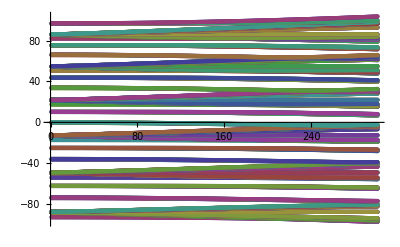

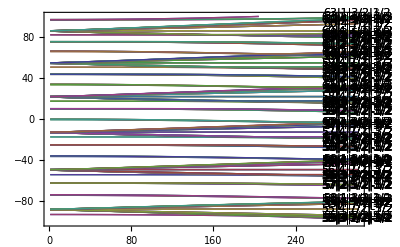

```mathematica
(*MultiListPlot: Generate Plot of Energies as a Function of EField*)
Clear[i,k,L,MPList,R]
MPList=Array[L,{Length[NList],2}];
Temp={};
EMIN=0;
EMAX=301;
ELabel=300;
Bfield =1*10^(-4); (* Magnetic field in Tesla *)
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)

E0=EMIN;
EStep=1;

For[i=1,i≤Length[NList],i++,MPList[[i]]={}];
Clear[i];
While[E0<EMAX,E0=E0+EStep;EField={0,E0,0};Temp=Eigenvalues[EI/10^9+BMatrix*Bfield*Subscript[μ, B]/h/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;For[i=1,i≤Length[NList],i++,MPList[[i]]=Join[MPList[[i]],{{E0,Temp[[i]]}}]  ]] ;
E0=EMIN;

Temp=Eigenvalues[EI/10^9+BMatrix*Bfield*Subscript[μ, B]/h/10^9+Subscript[e, SI]*Subscript[a, 0]*EMatrix.EField/h/10^9]-Subscript[E, 12]/10^9;(*Generate Labels for Levels*)
TempList=Array[T,Length[NList]];
For[i=1,i≤Length[NList],i++,TempList[[i]]={ELabel,Temp[[i]],LabelList[[i]]} ];
TempList

ListPlot[MPList]

Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-100,100}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

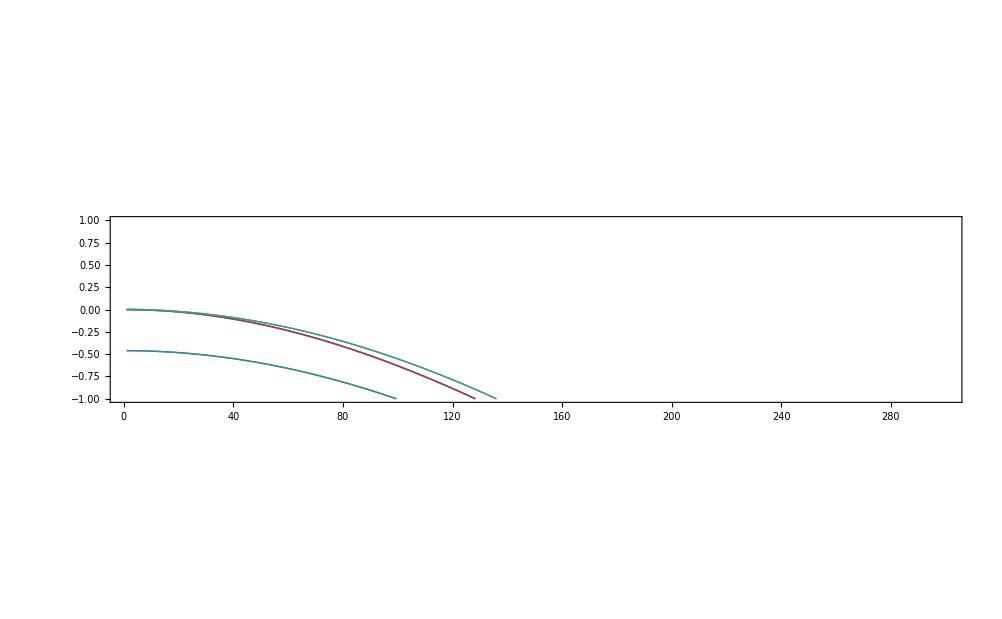

```mathematica
Show[ListPlot[MPList,Joined->True,PlotRange->{All,{-1,1}},Frame->True],Graphics[{Inset[TempList[[#,3]],{TempList[[#,1]],TempList[[#,2]]}]}&/@Range@Length@TempList]]
```

```mathematica
LabelList[[140]]

MPList[[140]]

(*MPListExport: Generate list to be read by Origin *)

Efieldlist = {};

E0=EMIN;


While[E0<EMAX,E0=E0+EStep;Efieldlist=Join[Efieldlist,{E0}]] ;
E0=EMIN;

Efieldlist


Clear[i,k,L,MPListExport,R]
NE0=(EMAX-EMIN)/EStep;
MPListExport=Array[0,{Length[NList],NE0}];
(*Electric Field in [V/m], Efield perpend. to BEC, so E={Ex,0,Ez=0}, parasitic Fields typ. 1V/cm, Const. Field typ. 5V/cm*)
(*Subscript[EStark, 12]=2*EMatrixelement[{44,0,1/2,1/2},{44,0,1/2,1/2}]*Subscript[e, SI]*Subscript[a, 0]*)(*Calculate shift of 44s44s-44s44s for R->∞ for Offset substraction in Plot, [J]*)



Clear[i];
j=0;
While[j<NE0,
j++;
For[i=1,i≤Length[NList],i++,
MPListExport[[i,j]]=MPList[[i,j,2]] 
 ]
] ;

MPListExport



Export["Stark_Shifts_around_60p3_2_mj3_2.dat",MPListExport]
Export["Electric_fields_for_Stark_Shifts_around_60p3_2_mj3_2.dat",Efieldlist]

(*Export["60p_j3_2_mj3_2_stark_Shift.dat",MPList[[218]]]*)
```

60|1|3/2|3/2

{{1,0.00273424},{2,0.00253929},{3,0.00221463},{4,0.00176064},{5,0.0011779},{6,0.000467174},{7,-0.00037056},{8,-0.00133406},{9,-0.00242181},{10,-0.00363198},{11,-0.00496243},{12,-0.00641072},{13,-0.00797416},{14,-0.00964996},{15,-0.0114354},{16,-0.0133279},{17,-0.0153254},{18,-0.0174266},{19,-0.0196307},{20,-0.0219374},{21,-0.0243471},{22,-0.0268604},{23,-0.029478},{24,-0.0322009},{25,-0.0350299},{26,-0.0379657},{27,-0.041009},{28,-0.0441603},{29,-0.0474203},{30,-0.0507891},{31,-0.0542673},{32,-0.0578549},{33,-0.0615523},{34,-0.0653594},{35,-0.0692765},{36,-0.0733036},{37,-0.0774406},{38,-0.0816877},{39,-0.0860448},{40,-0.0905117},{41,-0.0950886},{42,-0.0997752},{43,-0.104571},{44,-0.109477},{45,-0.114493},{46,-0.119617},{47,-0.124851},{48,-0.130194},{49,-0.135646},{50,-0.141207},{51,-0.146876},{52,-0.152654},{53,-0.15854},{54,-0.164533},{55,-0.170635},{56,-0.176845},{57,-0.183162},{58,-0.189586},{59,-0.196117},{60,-0.202755},{61,-0.2095},{62,-0.216351},{63,-0.223309},{64,-0.230372},{65,-0.237541},{66,-0.244816},{67,-0.252196},{68,-0.259681},{69,-0.267271},{70,-0.274965},{71,-0.282764},{72,-0.290667},{73,-0.298674},{74,-0.306784},{75,-0.314997},{76,-0.323314},{77,-0.331733},{78,-0.340255},{79,-0.348879},{80,-0.357605},{81,-0.366433},{82,-0.375362},{83,-0.384393},{84,-0.393524},{85,-0.402756},{86,-0.412088},{87,-0.42152},{88,-0.431052},{89,-0.440683},{90,-0.450413},{91,-0.460242},{92,-0.47017},{93,-0.480196},{94,-0.49032},{95,-0.500541},{96,-0.51086},{97,-0.521276},{98,-0.531788},{99,-0.542397},{100,-0.553102},{101,-0.563903},{102,-0.574799},{103,-0.58579},{104,-0.596876},{105,-0.608057},{106,-0.619331},{107,-0.6307},{108,-0.642161},{109,-0.653716},{110,-0.665364},{111,-0.677104},{112,-0.688937},{113,-0.700861},{114,-0.712876},{115,-0.724983},{116,-0.73718},{117,-0.749468},{118,-0.761846},{119,-0.774313},{120,-0.78687},{121,-0.799516},{122,-0.81225},{123,-0.825073},{124,-0.837984},{125,-0.850982},{126,-0.864067},{127,-0.877239},{128,-0.890498},{129,-0.903842},{130,-0.917272},{131,-0.930788},{132,-0.944388},{133,-0.958073},{134,-0.971842},{135,-0.985695},{136,-0.999631},{137,-1.01365},{138,-1.02775},{139,-1.04194},{140,-1.0562},{141,-1.07055},{142,-1.08498},{143,-1.09948},{144,-1.11407},{145,-1.12874},{146,-1.14349},{147,-1.15832},{148,-1.17322},{149,-1.1882},{150,-1.20326},{151,-1.2184},{152,-1.23361},{153,-1.2489},{154,-1.26427},{155,-1.27971},{156,-1.29523},{157,-1.31082},{158,-1.32648},{159,-1.34222},{160,-1.35803},{161,-1.37391},{162,-1.38986},{163,-1.40589},{164,-1.42199},{165,-1.43815},{166,-1.45439},{167,-1.47069},{168,-1.48707},{169,-1.50351},{170,-1.52002},{171,-1.53659},{172,-1.55323},{173,-1.56994},{174,-1.58672},{175,-1.60355},{176,-1.62045},{177,-1.63742},{178,-1.65444},{179,-1.67153},{180,-1.68868},{181,-1.70589},{182,-1.72316},{183,-1.74048},{184,-1.75787},{185,-1.77531},{186,-1.79281},{187,-1.81036},{188,-1.82797},{189,-1.84563},{190,-1.86334},{191,-1.88111},{192,-1.89893},{193,-1.91679},{194,-1.93471},{195,-1.95267},{196,-1.97068},{197,-1.98873},{198,-2.00683},{199,-2.02497},{200,-2.04315},{201,-2.06137},{202,-2.07963},{203,-2.09792},{204,-2.11626},{205,-2.13462},{206,-2.15302},{207,-2.17144},{208,-2.1899},{209,-2.20838},{210,-2.22689},{211,-2.24542},{212,-2.26396},{213,-2.28253},{214,-2.30111},{215,-2.3197},{216,-2.33831},{217,-2.35692},{218,-2.37553},{219,-2.39414},{220,-2.41275},{221,-2.43135},{222,-2.44995},{223,-2.46852},{224,-2.48708},{225,-2.50561},{226,-2.52412},{227,-2.54259},{228,-2.56102},{229,-2.5794},{230,-2.59773},{231,-2.616},{232,-2.63421},{233,-2.65234},{234,-2.67039},{235,-2.68834},{236,-2.7062},{237,-2.72394},{238,-2.74155},{239,-2.75903},{240,-2.77636},{241,-2.79353},{242,-2.81052},{243,-2.82731},{244,-2.84389},{245,-2.86023},{246,-2.87632},{247,-2.89214},{248,-2.90765},{249,-2.92284},{250,-2.93767},{251,-2.95212},{252,-2.96614},{253,-2.9797},{254,-2.99276},{255,-3.00526},{256,-3.01711},{257,-3.02791},{258,-3.03518},{259,-3.03907},{260,-3.04154},{261,-3.04279},{262,-3.0428},{263,-3.04152},{264,-3.03893},{265,-3.03498},{266,-3.02963},{267,-3.02288},{268,-3.01472},{269,-3.00513},{270,-2.99414},{271,-2.98176},{272,-2.96804},{273,-2.95301},{274,-2.93672},{275,-2.91922},{276,-2.90059},{277,-2.88088},{278,-2.86014},{279,-2.83846},{280,-2.81589},{281,-2.79249},{282,-2.76832},{283,-2.74345},{284,-2.71791},{285,-2.69177},{286,-2.66507},{287,-2.63786},{288,-2.61017},{289,-2.58204},{290,-2.55351},{291,-2.52461},{292,-2.49537},{293,-2.46582},{294,-2.43598},{295,-2.40588},{296,-2.37553},{297,-2.34496},{298,-2.31418},{299,-2.28321},{300,-2.25208},{301,-2.22078}}

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301}

{{-92.7988,-92.7989,-92.7991,-92.7993,-92.7996,-92.8,-92.8005,-92.801,-92.8016,-92.8022,-92.8029,-92.8037,-92.8046,-92.8055,-92.8065,-92.8076,-92.8087,-92.8099,-92.8112,-92.8125,«262»,-96.7756,-96.809,-96.8424,-96.8759,-96.9093,-96.9428,-96.9764,-97.0099,-97.0435,-97.0771,-97.1107,-97.1444,-97.178,-97.2117,-97.2455,-97.2792,-97.313,-97.3468,-97.3806},«288»,{«18»,«299»,«19»}}

Stark_Shifts_around_60p3_2_mj3_2.dat

Electric_fields_for_Stark_Shifts_around_60p3_2_mj3_2.dat